## Brian — PS 17 — 2025-04-11 — Solution

## EIWL3 Sections 39 and 40

## Exercises from EIWL3 Section 39

```mathematica
(* 39.1 *) {x, x+1, x+2, x^2}/.x->RandomInteger[100]
```

{98,99,100,9604}

```mathematica
(* 39.2 *) {x, x+1, x+2, x^2}/.x:>RandomInteger[100]
```

{14,51,54,1681}

## Exercises from EIWL3 Section 40

```mathematica
(* 40.1 *) f[x_]:=x^2
```

```mathematica
f[13]
```

169

```mathematica
(* 40.2 *) poly[n_Integer]:=Graphics[Style[RegularPolygon[n],Orange]]
```

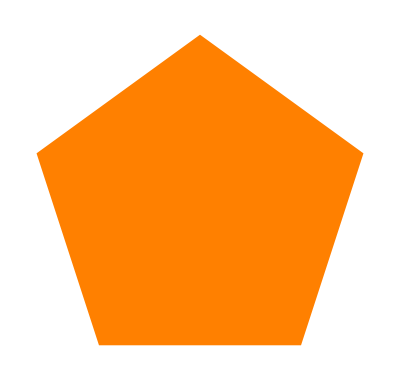

```mathematica
poly[5]
```

```mathematica
(* 40.3 *) reverse[{a_,b_}]:={b,a}
```

```mathematica
reverse[{"Bishop","Mammoth"}]
```

{Mammoth,Bishop}

```mathematica
(* 40.4 *) productOverSum[x_,y_]:=(x y)/(x+y)
```

```mathematica
productOverSum[2,3]
```

6/5

```mathematica
(* 40.5 *) sumDifferenceAndRatio[{first_,second_}]:={first+second,first-second,first/second}
```

```mathematica
sumDifferenceAndRatio[{99,11}]
```

{110,88,9}

```mathematica
(* 40.6 *) evenodd[0]= Red
```

RGBColor[1, 0, 0]

```mathematica
evenodd[n_Integer]:=If[EvenQ[n],Black,White]
```

```mathematica
evenodd/@Range[0,5]
```

{RGBColor[1, 0, 0],GrayLevel[1],GrayLevel[0],GrayLevel[1],GrayLevel[0],GrayLevel[1]}

```mathematica
(* 40.7 *) f[1,second_,third_]:=second+third
```

```mathematica
f[2,second_,third_]:=second third
```

```mathematica
f[3,second_,third_]:=second^third
```

```mathematica
f[#,3,5]&/@{1,2,3}
```

{8,15,243}

```mathematica
(* 40.8 *) f[0]=1;
```

```mathematica
f[1]=1;
```

```mathematica
f[n_Integer]:=f[n-1]+f[n-2]
```

```mathematica
f/@Range[5]
```

{1,2,3,5,8}

```mathematica
(* 40.9 *) animal[animal_String]:=Interpreter["Animal"][animal]["Image"]
```

```mathematica
animal["fox"]
```

-Graphics-

```mathematica
(* 40.10 *) nearwords[word_String,n_Integer]:=Nearest[WordList[],word,n]
```

```mathematica
nearwords["supercalifragilisticexpialidocious",5]
```

{materialistically,perspicacious,probabilistically,supercilious,superficiality}